```mathematica
params=Import["/home/tatjam/code/tfg/workdir/wagner_params.dat"];
liftTime=Import["/home/tatjam/code/tfg/workdir/wagner_lift_over_time.dat"][[1]];
```

```mathematica
longTerm=Import["/home/tatjam/code/tfg/workdir/wagner_long_term_forces.dat"][[1]];
```

```mathematica
tstep=params[[3]][[1]];
steps=params[[4]][[1]];
```

```mathematica
ts=Table[tstep*i, {i, 0,steps-1}]; (* Tiempos dimensionales *)
AoA=params[[2]][[1]];
vel=params[[1]][[1]];
chord=0.25;
tadim=ts*vel/chord;
```

```mathematica
adimts=2*vel/chord*ts;
```

Lift ideal generado por el perfil, vs lift según el método de paneles

```mathematica
steadyLift=longTerm[[2]];
```

Solución de Wagner teórica

```mathematica
wagner=1-0.165*Exp[-0.0455*adimts/2]-0.335*Exp[-0.3*adimts/2];
```

Función que permite combinar datos brutos y los tiempos adimensionales

```mathematica
dataWithTime[data_,time_]:=
Thread[{#2,#1}&[data,time]]
```

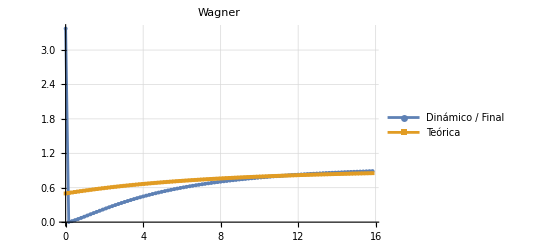

```mathematica
ListLinePlot[{
dataWithTime[liftTime/steadyLift,adimts],
dataWithTime[wagner, adimts]},
PlotLegends->{"Dinámico / Final","Teórica"},PlotRange->{All,All},PlotMarkers->{Automatic, 4},
PlotLabel->"Wagner",GridLines->Automatic]
```